Remove::rmnsm: There are no symbols matching ""Global`*"".

{}

{}

{1001}

{1001}

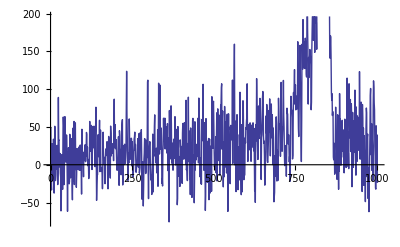

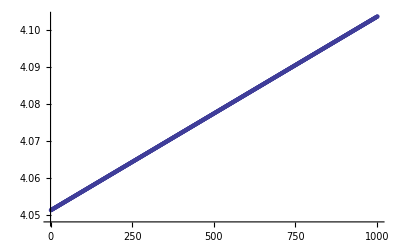

{y}

{v}

```mathematica
Remove["Global`*"]
Unprotect[y]
Unprotect[v]
y=Flatten[Import["C:\\Data\\y.csv"]];
v=Flatten[Import["C:\\Data\\v.csv"]];
Dimensions[v]
Dimensions[y]
ListLinePlot[y]
ListPlot[v]
Protect[y]
Protect[v]
```

Remove::rmptc: Symbol v is Protected and cannot be removed.

Remove::rmptc: Symbol y is Protected and cannot be removed.

A9+A0 ⅇ^(-(0.5 (-4.09443+x)^2)/A2^2)+A3 ⅇ^(-(0.5 (-4.09276+x)^2)/A5^2)+A6 ⅇ^(-(0.5 (-4.09238+x)^2)/A8^2)

{1001,2}

{A0→199.81,A1→4.09443,A2→0.00125732,A3→129.773,A4→4.09276,A5→0.00237591,A6→-66.6033,A7→4.09238,A8→0.00143043,A9→20.1936}

20.1936+199.81 ⅇ^(-316284. (-4.09443+x)^2)+129.773 ⅇ^(-88574.6 (-4.09276+x)^2)-66.6033 ⅇ^(-244364. (-4.09238+x)^2)

6.7312+199.81 ⅇ^(-316284. (-4.09443+x)^2)

6.7312+129.773 ⅇ^(-88574.6 (-4.09276+x)^2)

6.7312-66.6033 ⅇ^(-244364. (-4.09238+x)^2)

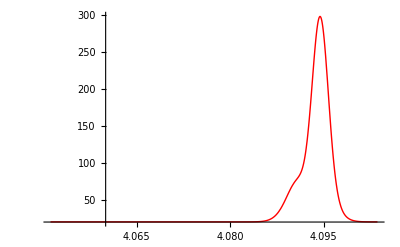

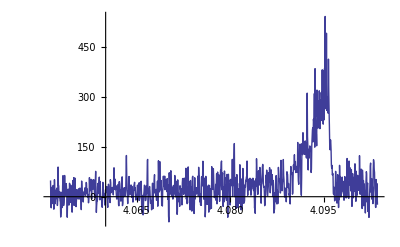

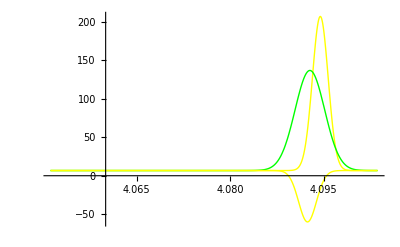

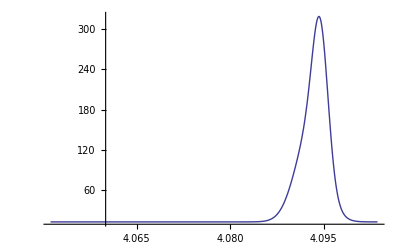

ListLinePlot::lpn: res is not a list of numbers or pairs of numbers.

ListLinePlot[res]

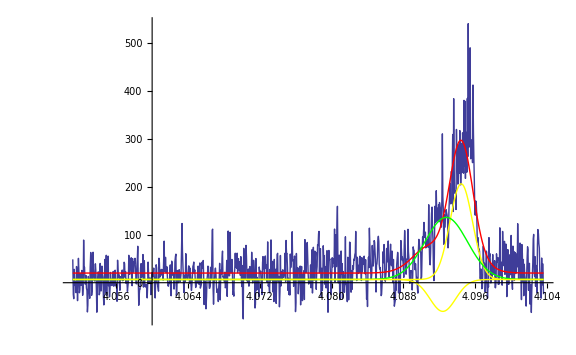

```mathematica
Remove["Global`*"]
Gaussian[x_,A_,xo_,σ_]=A ⅇ^(-(0.5(x-xo)^2)/σ^2);

data=Table[{v[[i]],y[[i]]},{i,1,1001}];
function=Gaussian[x,A0,4.09443,A2]+Gaussian[x,A3,4.09276,A5]+Gaussian[x,A6,4.09238,A8]+A9
Dimensions[data]

nlm=FindFit[data,function,{{A0,300},{A1,4.09443},{A2,.0007},{A3,300},{A4,4.09276},{A5,.0018},{A6,300},{A7,4.09238},{A8,.0008},{A9,20}},x,MaxIterations->∞]
(*FIT[x_]=nlm["BestFit"]*)
FIT[x_]=function/.nlm
(*A=nlm["BestFitParameters"]
res=nlm["FitResiduals"];
chi=nlm["EstimatedVariance"]*)
(*χsqred=chi/(1001-7)*)
(*χsq=(Sum[(y[[i]]-FIT[v[[i]]])^2,{i,1,1001}]/(StandardDeviation[y]^2))*)
g1[x_]=Gaussian[x,A0,A1,A2]+A9/3/.nlm
g2[x_]=Gaussian[x,A3,A4,A5]+A9/3/.nlm
g3[x_]=Gaussian[x,A6,A7,A8]+A9/3/.nlm
p1=Plot[FIT[x],{x,Min[v],Max[v]},PlotRange->All,PlotStyle->{Thick,Red},PlotRange->All]
p2=ListLinePlot[data,PlotRange->All]
p3=Plot[{g1[x],g2[x],g3[x]},{x,Min[v],Max[v]},PlotRange->All,PlotStyle->{Yellow,Green},PlotStyle->Thick]
p4=Plot[g1[x]+g2[x],{x,Min[v],Max[v]},PlotRange->All]
ListLinePlot[res]
Show[p2,p1,p3,PlotRange->All,ImageSize->Large]
```